```mathematica
{euRoul=Import["http://www.onlinecasinoreporter.com/wp-content/uploads/2012/07/european-roulette-table.gif"],
usRoul=Import["http://www.roulette-games.com/images/american_roulette_layout.gif"]};
```

```mathematica
(* todo: parse number in string to number
todo: Handle erros of incorrrect inputs 

--- spins the wheel and if win occurs, returns amount to multiply original bet by, otherwise returns -1
*)
simSpin[roulType_,betName_]:=Module[{denom=Switch[roulType,"enRoul",37,"usRoul",38,_,Abort[]],winOrLose,mult,oneToOneDist,twoToOneDist,straightUp},
oneToOneDist=BinomialDistribution[1,18/denom];
twoToOneDist=BinomialDistribution[1,12/denom];
straightUp=BinomialDistribution[1,1/denom];

(* A few possibilities of bets...*)
If[StringQ[betName],
If[StringMatchQ[betName,{"1to18","even","red","black","odd","19to36"},IgnoreCase->True], winOrLose=RandomVariate[oneToOneDist];mult=1;];
If[StringMatchQ[betName,{"1st12","2nd12","3rd12","2to1"},IgnoreCase->True], winOrLose=RandomVariate[twoToOneDist];mult=2;];
,(* Else, bet is single numbers 0 to 36*)
winOrLose=RandomVariate[straightUp]; mult=35;];
If[winOrLose==1,mult,-1]
]
```

### Runs one trial with specified global parameters in: gameSettings and simulationSettings Type strategy here

```mathematica
runTrial[]:=Module[{bankHistory={gameSettings["bankRoll"]},betAmount=gameSettings["minBet"],betType="black"},
Do[
(* simulate roulette spin with given bet and append result to bankHistory*)
bankHistory=Append[bankHistory, Last[bankHistory]+betAmount*simSpin[gameSettings["rouletteType"], betType]];

(* betting strategy here .... changes bet amount or betType*)
(*If[Part[bankHistory,-1]-Part[bankHistory,-2]> 0,betAmount=gameSettings["minBet"], betAmount*=1];*) (* constant bet size*)
If[Part[bankHistory,-1]-Part[bankHistory,-2]> 0,betAmount=gameSettings["minBet"], betAmount*=2]; (* double after every loss*)


(* Game boundries:
 - Can't have negative bankroll
- Can't bet more than we have (bet all we have instead)
- Must stay within max/min betting limits  
*)
If[(Last[bankHistory]≤ 0 ), Break[]];
If[betAmount> Last[bankHistory],betAmount=Last[bankHistory]];
betAmount=betAmount/.{x_/;x<gameSettings["minBet"]->gameSettings["minBet"],x_/;x>gameSettings["maxBet"]->gameSettings["maxBet"]};


,simulationSettings["gamesPerTrial"]];

(* Return bank history *)
bankHistory
]
```

```mathematica
gameSettings=<| "rouletteType"-> "usRoul", "bankRoll"->10000, "minBet"->5, "maxBet"->1000, "initialBet"->5|>;
simulationSettings=<|"gamesPerTrial"-> 1000, "numOfTrials"->100|>;
```

Summary:

Games per trial:  | 1000
Number of trials:  | 100
% of bankrupcies:  | 4.
Average earnings:  | -1141.15
Average final bankroll:  | 8858.85
Expected value :  | -1.14115
95% CI of E(x) +-:  | 6.41449

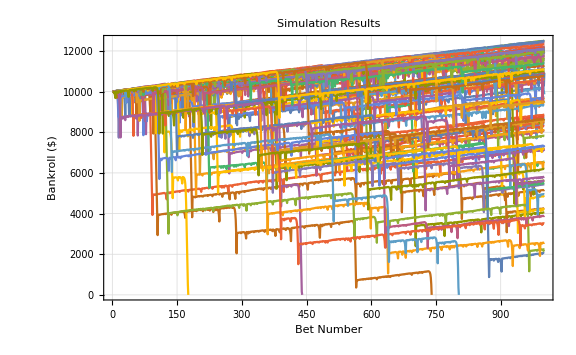

```mathematica
trialHistory={};
finalBankRoll={};
gameHistory={};
trialNum=0;

PrintTemporary["Running simulation..."];
PrintTemporary[ProgressIndicator[Dynamic[trialNum],{0,simulationSettings["numOfTrials"]}]];
Table[
singleGameHistory=runTrial[];

(* snarf relevant data from trial for later analysis *)
finalBankRoll=Append[finalBankRoll, Last[singleGameHistory]];
trialHistory=Append[trialHistory, singleGameHistory];

trialNum++;
,simulationSettings["numOfTrials"]];

Print[Style["Summary:",Bold,16]];
stdev=N[StandardDeviation[finalBankRoll]];
varian=N[Variance[finalBankRoll]];
expVal=N[Mean[finalBankRoll-gameSettings["bankRoll"]]/simulationSettings["gamesPerTrial"]];
stdevExpVal=N[StandardDeviation[(finalBankRoll-gameSettings["bankRoll"])/simulationSettings["gamesPerTrial"]]];

Grid[{
{"Games per trial: ", simulationSettings["gamesPerTrial"]},
{"Number of trials: ", simulationSettings["numOfTrials"]},
{"% of bankrupcies: ", N[Count[finalBankRoll,0]/simulationSettings["numOfTrials"]]*100},
{"Average earnings: ",  N[Mean[finalBankRoll]-gameSettings["bankRoll"]]},
{"Average final bankroll: ", N[Mean[finalBankRoll]]},
{"Expected value : ", expVal},
{"95% CI of E(x) +-: ", (1.96*stdevExpVal)}

},Frame->All,Background->{{LightGray}}]

PrintTemporary["Plotting results..."];
ListLinePlot[trialHistory,GridLines->Automatic,PlotRange->All,PlotLabel->"Simulation Results",
BaseStyle->{FontWeight->"Bold",FontSize->15},
Axes->True,Frame->True,
FrameLabel->{"Bet Number","Bankroll ($)"},
ImageSize->Large]
(* Expected Value of betting black is:
N[18/38-20/38]*5
 -0.053.* 5 =  -0.2631578947368421 *)
```